```mathematica
n=100
Sum[(n!n^(n-k-1))/((n-k)!),{k,1,n}]
```

100

12209960630215980300253132956815012998412714159392662223854992521128809374822896606879062793565756480077431168694642794552798934366694577253573013735421843845957043306726309232640000000000000000000000

```mathematica
100^100
```

100000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mkh19\Desktop\Projects\untitled1

```mathematica
str = OpenRead["res.txt"]
ls = ReadList[str,Number]
```

InputStream[…]

{1.,1.25,1.40741,1.52344,1.61568,1.69239,1.75812,1.81567,1.86688,1.91303,1.95504,1.9936,2.02925,2.06239,2.09336,2.12244,2.14984,2.17574,2.20031,2.22368,2.24596,2.26724,2.28762,2.30716,2.32594,2.34402,2.36144,2.37824,2.39449,2.4102,2.42541,2.44016,2.45447,2.46837,2.48188,2.49502,2.50782,2.52028,2.53243,2.54428,2.55585,2.56715,2.5782,2.58899,2.59955,2.60989,2.62001,2.62992,2.63964,2.64659}

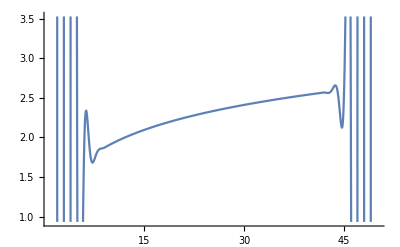

```mathematica
Plot[(InterpolatingPolynomial[ls,x]),{x,1,50}]
```

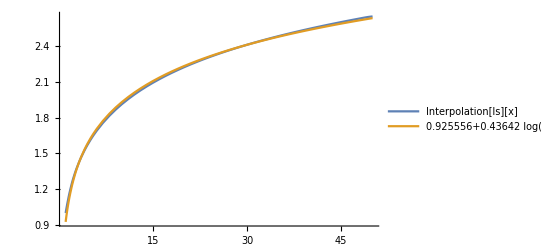

```mathematica
Plot[{(Interpolation[ls])[x],Evaluate@Fit[ls,{1, Log[x]},x]},{x,1,50}, PlotLegends->"Expressions"]
```

```mathematica
Fit[ls,{1,Log[x]},x]
```

Power::infy: Infinite expression 1/0. encountered.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Fit[{1.,1.25,1.40741,1.52344,1.61568,1.69239,1.75812,1.81567,1.86688,1.91303,1.95504,1.9936,2.02925,2.06239,2.09336,2.12244,2.14984,2.17574,2.20031,2.22368,2.24596,2.26724,2.28762,2.30716,2.32594,2.34402,2.36144,2.37824,2.39449,2.4102,2.42541,2.44016,2.45447,2.46837,2.48188,2.49502,2.50782,2.52028,2.53243,2.54428,2.55585,2.56715,2.5782,2.58899,2.59955,2.60989,2.62001,2.62992,2.63964,2.64659},{1,0.165514/Log[x]},x]

```mathematica
2^1/4
```

1/2

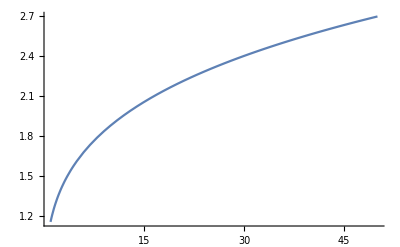

```mathematica
Plot[Evaluate@Fit[ls,{1,x^(1/4)},x],{x,1,50}]
```

```mathematica
Log[2,1.25]
```

0.321928

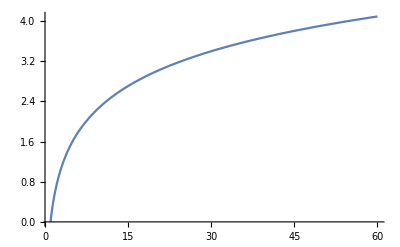

```mathematica
Plot[Log[x],{x,1,60}]
```

```mathematica
Solve[Log[2,x]==1/4,x]
```

{{x→2^(1/4)}}

```mathematica
2^(1/4)
```

1.18921